```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define parameters*)
delay=1;
t=1;

(*Define the equation*)
(*v=(J0+Sqrt[J0^2-4*(J0-e)])/2;*)
J=J1/2;
A=((J*y-2*v)/(-2*t-2*v*t^2));
eq=A*(1+4*v*t-A*t^2)^2-J^2*(1-y^2)==0;

(*Write as cubic in y*)
collectedEq=Collect[Expand[eq],y, Simplify]
```

(-J1^2 (1+v)^3+4 v (1+2 v)^4)/(4 (1+v)^3)-(J1 (1+2 v)^2 (1+2 v+4 v^2) y)/(4 (1+v)^3)+(J1^2 (2+5 v+4 v^2+4 v^3) y^2)/(16 (1+v)^3)-(J1^3 y^3)/(64 (1+v)^3)==0

```mathematica
(*Now solve for roots of the cubic*)
solutions = FullSimplify[Solve[collectedEq,y]];
sol1=y/. solutions[[1]];
sol2=y/. solutions[[2]];
sol3=y/. solutions[[3]];

(*Plug in parameter expression for v*)
y1[J0_,J1_,e_]:=Evaluate[sol1/. {v->(J0+Sqrt[J0^2-4*(J0-e)])/2}];
y2[J0_,J1_,e_]:=Evaluate[sol2/. {v->(J0+Sqrt[J0^2-4*(J0-e)])/2}];
y3[J0_,J1_,e_]:=Evaluate[sol3/. {v->(J0+Sqrt[J0^2-4*(J0-e)])/2}];
```

```mathematica
(*Plot*)
etest=2;
GraphicsRow[{
DensityPlot[Re[y1[J0,J1,etest]],{J0,-10,10},{J1,-20,20},ColorFunction->"TemperatureMap",
PlotRange->{-1,1},
PlotLegends->Automatic,
FrameLabel->{"J0","J1"},PlotLabel->"Re[y1]"],
DensityPlot[Im[y1[J0,J1,etest]],{J0,-10,10},{J1,-20,10},ColorFunction->"TemperatureMap",
PlotRange->{-.1,.1},
PlotLegends->Automatic,
FrameLabel->{"J0","J1"},PlotLabel->"Im[y1]"]
},ImageSize->Large]

GraphicsRow[{
DensityPlot[Re[y2[J0,J1,etest]],{J0,-10,10},{J1,-1000,1000},ColorFunction->"TemperatureMap",
PlotRange->{-1,1},
PlotLegends->Automatic,FrameLabel->{"J0","J1"},PlotLabel->"Re[y2]"],
DensityPlot[Im[y2[J0,J1,etest]],{J0,-10,10},{J1,-1000,1000},ColorFunction->"TemperatureMap",
PlotRange->{-.1,.1},
PlotLegends->Automatic,FrameLabel->{"J0","J1"},PlotLabel->"Im[y2]"]
},ImageSize->Large]

GraphicsRow[{
DensityPlot[Re[y3[J0,J1,etest]],{J0,-10,10},{J1,-1000,1000},ColorFunction->"TemperatureMap",
PlotRange->{-1,1},
PlotLegends->Automatic,
FrameLabel->{"J0","J1"},PlotLabel->"Re[y3]"],
DensityPlot[Im[y3[J0,J1,etest]],{J0,-10,10},{J1,-1000,1000},ColorFunction->"TemperatureMap",
PlotRange->{-.1,.1},
PlotLegends->Automatic,FrameLabel->{"J0","J1"},PlotLabel->"Im[y3]"]
},ImageSize->Large]
```

-Graphics-

-Graphics-

-Graphics-

turingHopf_zero_contour.csv

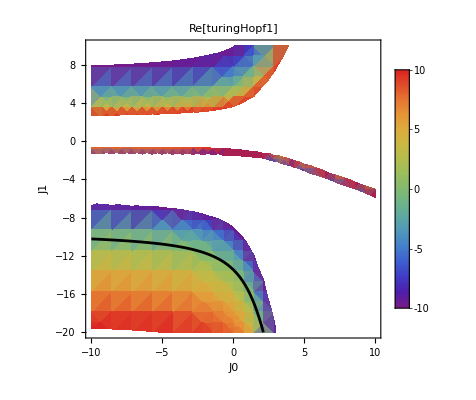

```mathematica
etest1=2;
vfunc[J0_,e_]:=(J0+Sqrt[J0^2-4*(J0-e)])/2;
turingHopf1[J0_,J1_,e_]:=Simplify[((1/delay)*ArcCos[y1[J0,J1,e]])^2*(-2t-2*vfunc[J0,e]*t^2)-(J1/2)*y1[J0,J1,e]+2*vfunc[J0,e]];
(*DensityPlot for the real part*)densityPlot=DensityPlot[Re[turingHopf1[J0,J1,etest1]],{J0,-10,10},{J1,-20,10},ColorFunction->"Rainbow",PlotRange->{-10,10},ColorFunctionScaling->True,PlotLegends->BarLegend[{"Rainbow",{-10,10}}],FrameLabel->{"J0","J1"},PlotLabel->"Re[turingHopf1]"];

(*ContourPlot where Re[turingHopf1]==0*)
zeroContour=ContourPlot[Re[turingHopf1[J0,J1,etest1]]==0,{J0,-10,10},{J1,-20,-6},ContourStyle->{Thick,Black},Contours->{0},PlotPoints->100,MaxRecursion->4,Frame->False,Axes->False,PlotRangePadding->None];
lines=Cases[Normal[zeroContour],Line[pts_]:>pts,Infinity];
contourPoints=Flatten[lines,1];
Export["turingHopf_zero_contour.csv",contourPoints]

(*Combine them*)
Show[densityPlot,zeroContour]
(*DensityPlot[Im[turingHopf1[J0,J1,etest1]],{J0,-10,10},{J1,-20,10},
ColorFunction->"Rainbow",
PlotRange->{-.1,.1},
PlotLegends->BarLegend[{"Rainbow",{-.1,.1}}],
FrameLabel->{"J0","J1"},
PlotLabel->"Im[turingHopf1]"]*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["turingHopf_zero_contour.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["turingHopf_zero_contour.csv"]]]
```

```mathematica
etest1=-2;
vfunc[J0_,e_]:=(J0+Sqrt[J0^2-4*(J0-e)])/2;
turingHopf1[J0_,J1_,e_]:=Simplify[((1/delay)*ArcCos[y1[J0,J1,e]])^2*(-2t-2*vfunc[J0,e]*t^2)-(J1/2)*y1[J0,J1,e]+2*vfunc[J0,e]];
(*DensityPlot for the real part*)densityPlot=DensityPlot[Re[turingHopf1[J0,J1,etest1]],{J0,5,10},{J1,-60,10},ColorFunction->"Rainbow",PlotRange->{-10,10},ColorFunctionScaling->True,PlotLegends->BarLegend[{"Rainbow",{-10,10}}],FrameLabel->{"J0","J1"},PlotLabel->"Re[turingHopf1]"];

(*ContourPlot where Re[turingHopf1]==0*)
zeroContour=ContourPlot[Re[turingHopf1[J0,J1,etest1]]==0,{J0,5,10},{J1,-60,-6},ContourStyle->{Thick,Black},Contours->{0},PlotPoints->100,MaxRecursion->4,Frame->False,Axes->False,PlotRangePadding->None];
lines=Cases[Normal[zeroContour],Line[pts_]:>pts,Infinity];
contourPoints=Flatten[lines,1];
Export["turingHopf_zero_contour_belowThres.csv",contourPoints]

(*Combine them*)
Show[densityPlot,zeroContour]
```

turingHopf_zero_contour_belowThres.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["turingHopf_zero_contour_belowThres.csv"]]]
```